## Cubic Spline 1

```mathematica
Clear[ff,f,fff]
```

```mathematica
b1=0;b2=0.2;b3=1;
c1=0;c2=0.5;c3=1;
lo=1;
```

```mathematica
f[x_/;b1≤Abs[x]/lo≤b2]=1-15/lo^2*x^2+30/lo^3*Abs[x]^3;
f[x_/;b2≤Abs[x]/lo≤ b3]=1.25*(1-Abs[x]/lo)^3;
f[x_/;b3≤Abs[x]/lo]=0;
```

```mathematica
ff[x_/;b1≤Abs[x]/lo≤b2]=-30/lo^2*x+90/lo^3*Sign[x]*x^2;
ff[x_/;b2≤Abs[x]/lo≤ b3]=-3.75/lo*Sign[x]*(1-Abs[x]/lo)^2;
ff[x_/;b3≤Abs[x]/lo]=0;
```

```mathematica
fff[x_/;b1≤Abs[x]/lo≤b2]=-30/lo^2+180/lo^3*Abs[x];
fff[x_/;b2≤Abs[x]/lo≤ b3]=7.5/lo^2*(1-Abs[x]/lo);
fff[x_/;b3≤Abs[x]/lo]=0;
```

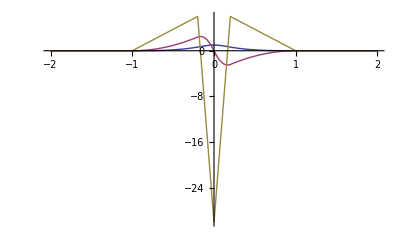

```mathematica
Plot[{f[x],ff[x],fff[x]},{x,-2,2},PlotRange->Full]
```

## Cubic Spline 2

```mathematica
Clear[ff,f,fff]
```

```mathematica
b1=0;b2=0.2;b3=1;
c1=0;c2=0.5;c3=1;
lo=1;
```

```mathematica
f[x_/;c1≤Abs[x]/lo≤c2]=1-6/lo^2*x^2+6/lo^3*Abs[x]^3;
f[x_/;c2≤Abs[x]/lo≤ b3]=2*(1-Abs[x]/lo)^3;
f[x_/;c3≤Abs[x]/lo]=0;
```

```mathematica
ff[x_/;c1≤Abs[x]/lo≤c2]=-12/lo^2*x+18/lo^3*Sign[x]*x^2;
ff[x_/;c2≤Abs[x]/lo≤ c3]=-6/lo*Sign[x]*(1-Abs[x]/lo)^2;
ff[x_/;c3≤Abs[x]/lo]=0;
```

```mathematica
fff[x_/;c1≤Abs[x]/lo≤c2]=-12/lo^2+36/lo^3*Abs[x];
fff[x_/;c2≤Abs[x]/lo≤ c3]=12/lo^2*(1-Abs[x]/lo);
fff[x_/;c3≤Abs[x]/lo]=0;
```

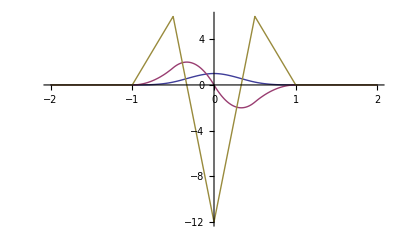

```mathematica
Plot[{f[x],ff[x],fff[x]},{x,-2,2},PlotRange->Full]
```